```mathematica
(*http://openclassroom.stanford.edu/MainFolder/DocumentPage.php?course=DeepLearning&doc=exercises/ex2/ex2.html*)
```

```mathematica
(*http://www.cnblogs.com/elaron/archive/2013/05/21/3090724.html*)
(*http://www.cnblogs.com/elaron/archive/2013/05/20/3088894.html Normal Equations 的由来*)
```

```mathematica
(*http://mathematica.stackexchange.com/questions/3242/can-mathematica-do-symbolic-linear-algebra*)
```

```mathematica
(*see help doc - How to / Perform a Linear Regression*)
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
import[fname_]:=ReadList[fname,String]//ImportString@@{#,"CSV"}&/@#&//Flatten
```

```mathematica
xs=import["ex2x.dat"]
```

{2.06587,2.36841,2.53999,2.54208,2.54908,2.78669,2.91168,3.03563,3.11467,3.15824,3.32759,3.37932,3.4122,3.42158,3.53157,3.6393,3.67325,3.92565,4.04986,4.24833,4.34401,4.38265,4.42306,4.61024,4.68812,4.97773,5.036,5.06845,5.41615,5.43956,5.45632,5.56985,5.60157,5.68776,5.72156,5.85389,6.1978,6.35109,6.4797,6.73838,6.86377,7.02234,7.07824,7.15142,7.4664,7.59739,7.74407,7.77297,7.82645,7.93064}

```mathematica
ys=import["ex2y.dat"]
```

{0.779189,0.915968,0.905384,0.905661,0.938989,0.966847,0.964368,0.914459,0.939339,0.96075,0.898371,0.912097,0.942385,0.966246,1.05265,1.01438,0.959694,0.968537,1.07661,1.1455,1.03406,1.007,0.966836,1.08959,1.06345,1.12372,1.03234,1.08745,1.0703,1.16065,1.0778,1.10698,1.09719,1.16486,1.14118,1.08442,1.12525,1.11683,1.19708,1.20695,1.1251,1.12357,1.21328,1.25227,1.24971,1.17997,1.18973,1.30299,1.26011,1.25623}

```mathematica
data= MapThread[List,{xs,ys}]
```

{{2.06587,0.779189},{2.36841,0.915968},{2.53999,0.905384},{2.54208,0.905661},{2.54908,0.938989},{2.78669,0.966847},{2.91168,0.964368},{3.03563,0.914459},{3.11467,0.939339},{3.15824,0.96075},{3.32759,0.898371},{3.37932,0.912097},{3.4122,0.942385},{3.42158,0.966246},{3.53157,1.05265},{3.6393,1.01438},{3.67325,0.959694},{3.92565,0.968537},{4.04986,1.07661},{4.24833,1.1455},{4.34401,1.03406},{4.38265,1.007},{4.42306,0.966836},{4.61024,1.08959},{4.68812,1.06345},{4.97773,1.12372},{5.036,1.03234},{5.06845,1.08745},{5.41615,1.0703},{5.43956,1.16065},{5.45632,1.0778},{5.56985,1.10698},{5.60157,1.09719},{5.68776,1.16486},{5.72156,1.14118},{5.85389,1.08442},{6.1978,1.12525},{6.35109,1.11683},{6.4797,1.19708},{6.73838,1.20695},{6.86377,1.1251},{7.02234,1.12357},{7.07824,1.21328},{7.15142,1.25227},{7.4664,1.24971},{7.59739,1.17997},{7.74407,1.18973},{7.77297,1.30299},{7.82645,1.26011},{7.93064,1.25623}}

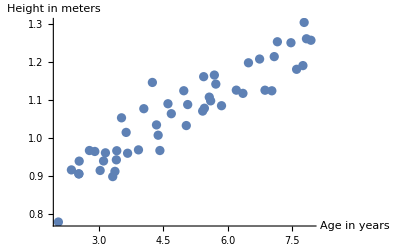

```mathematica
ListPlot[data,AxesLabel->{"Age in years","Height in meters"}]
```

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[0.750163+0.0638812 x]

```mathematica
model["BestFit"]
```

0.750163+0.0638812 x

```mathematica
(*http://www.cnblogs.com/tornadomeet/archive/2013/03/15/2961660.html*)
(*所得数值和上面的link中“采用normal equations方法求解”给出的数值一至*)
```

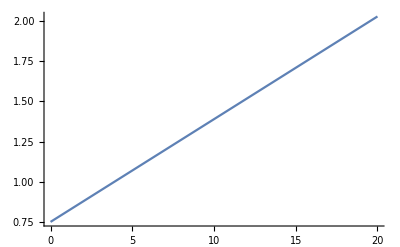

```mathematica
Plot[model["BestFit"], {x, 0, 20}]
```

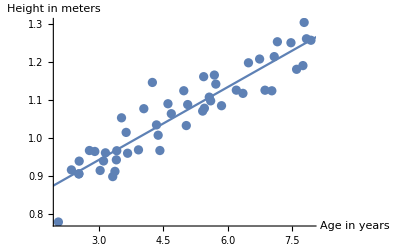

```mathematica
Show[ListPlot[data,AxesLabel->{"Age in years","Height in meters"}], Plot[model["BestFit"], {x, 0, 30}]]
```

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.750163 | 0.0195458 | 38.3797 | 1.10767×10^-37
x | 0.0638812 | 0.00375008 | 17.0346 | 5.50999×10^-22